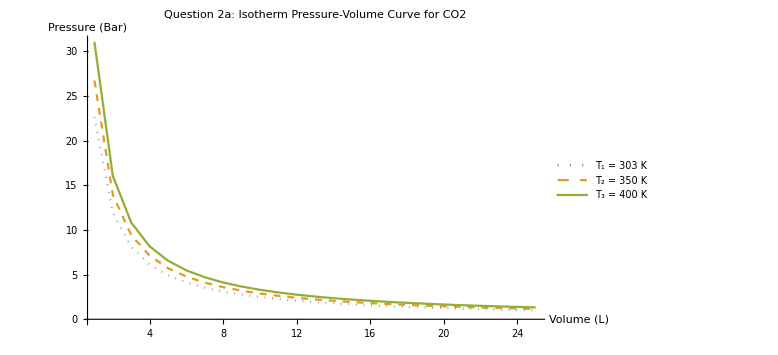

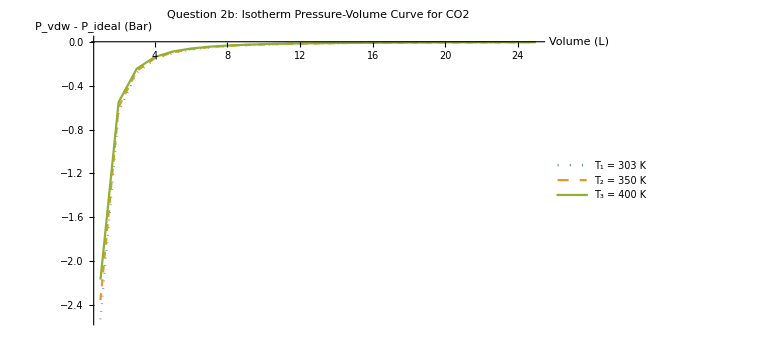

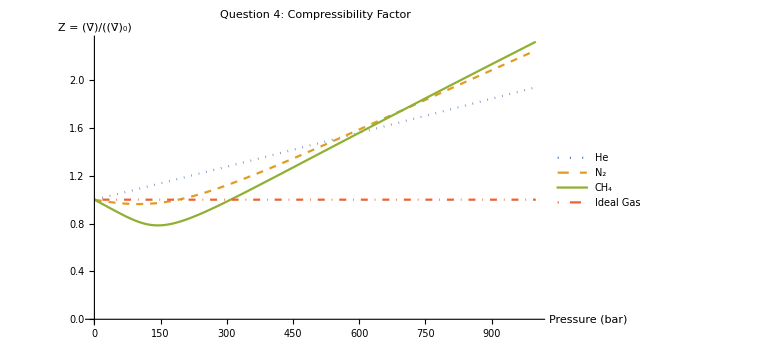

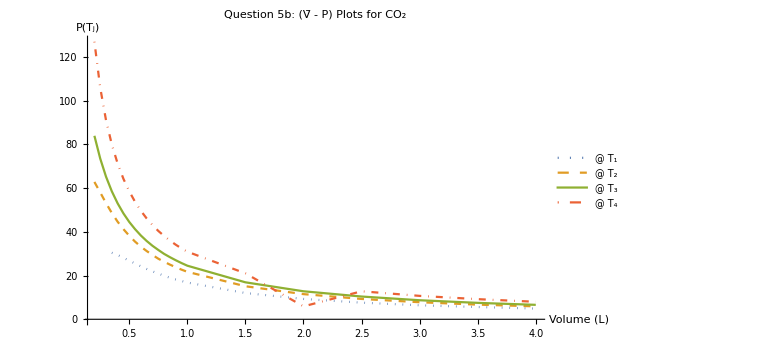

Parameters for T_1:{B_2→216.583,B_3→-62.6143}

Parameters for T_2:{B_2→160.26,B_3→-26.9935}

Parameters for T_3:{B_2→184.247,B_3→-29.8556}

Parameters for T_4:{B_2→237.669,B_3→-36.6128}

Question 5c: Temperatures for each isotherm:

T_1 = 235.733 K

T_2 = 283.841 K

T_3 = 317.518 K

T_4 = 384.87 K

```mathematica
(*
Lab: Equations of State M8
Author: Jared Frazier
Description:

Reproduce isotherm and compressibility factor figures from Physical Chemistry: A Molecular Approach (1997).

Course: CHEM 4361
*)
Clear["Global`*"]

(***********************)
(*Question 2: Isotherms*)
(***********************)
(*Gas constant in (L * bar)/(mol * K)*)
universalGasConstR = 0.083145;

pressureVdwFuncOfVandT[a_, b_, temp_, vol_] := (
(*
The van der Wals equation P (V, T)
:param a: Gas constant 'a' ((L^2 bar)/mol^2)
:param b: Gas constant 'b' (L/mol)
:param temp: Temperature (K) 
:param vol: Volume (liter)
:return: Pressure (bar)
*)
	(universalGasConstR * temp)/(vol - b)- a/(vol * vol)
)
pressureIdealGas[temp_, vol_] := (
(*
The pressure for an ideal gas
:param temp: Temperature (K)
:param vol: Volume (L)
:return: Pressure (bar)
*)
	(universalGasConstR * temp)/vol
)

(*Gas constants for Subscript[CO, 2]*)
vdwConstsForCO2 = ChemicalData["CarbonDioxide", "VanDerWaalsConstants"] ;
aConstCO2 = vdwConstsForCO2[[1, 1]];
bConstCO2 = vdwConstsForCO2[[2, 1]];
(*Pressure Volume Plots*)

(*For both plots*)
volumeListForPlot = Range[1, 25];
t1 = 303;
t2 = 350;
t3 = 400;

(*Plot Subscript[P, vdw]*)
t1Pressures = pressureVdwFuncOfVandT[aConstCO2, bConstCO2, t1, volumeListForPlot];
t2Pressures = pressureVdwFuncOfVandT[aConstCO2, bConstCO2, t2, volumeListForPlot];
t3Pressures = pressureVdwFuncOfVandT[aConstCO2, bConstCO2, t3, volumeListForPlot];
ListLinePlot[
	{t1Pressures, t2Pressures, t3Pressures},
	PlotLabel->"Question 2a: Isotherm Pressure-Volume Curve for CO2",
	AxesLabel->{"Volume (L)", "Pressure (Bar)"},
	PlotLegends->{"T_1 = 303 K", "T_2 = 350 K", "T_3 = 400 K"},
	PlotStyle->{Dotted, Dashed, Thick},
	PlotRange->Full,
	ImageSize->Large
]

(*Plot Subscript[P, vdw] - Subscript[P, ideal]*)
t1PressuresIdeal = pressureIdealGas[t1, volumeListForPlot];
t2PressuresIdeal = pressureIdealGas[t2, volumeListForPlot];
t3PressuresIdeal = pressureIdealGas[t3, volumeListForPlot];
ListLinePlot[
	{t1Pressures - t1PressuresIdeal, t2Pressures - t2PressuresIdeal, t3Pressures - t3PressuresIdeal},
	PlotLabel->"Question 2b: Isotherm Pressure-Volume Curve for CO2",
	AxesLabel->{"Volume (L)", "P_vdw - P_ideal (Bar)"},
	PlotLegends->{"T_1 = 303 K", "T_2 = 350 K", "T_3 = 400 K"},
	PlotStyle->{Dotted, Dashed, Thick},
	PlotRange->Full,
	ImageSize->Large
]
(*****************************************)
(*Question 3: Function for Molar Volume*)
(*****************************************)
vdwExpression = (P + a/V^2)*(V - b) - R*T;   (*From eq (7) in the handout*)
vdwVolumeExpression = Solve[vdwExpression==0, V];  (*Set to 0 and solve for Volume*)
realVdwVolumeExpression = V/. vdwVolumeExpression[[1, 1]];  (*The only real solution expression*)
molarVolumeRealFunction[a_, b_, P_, R_, T_] := (
(*
Given several gas arguments, return the real molar volume of the gas.
:param a: Gas Constant.
:param b: Gas Constant.
:param P: Pressure (Bar).
:param R: Universal Gas Constant.
:param T: Temperature (K).
:return: The real molar volume of the gas.
*)
	Evaluate[realVdwVolumeExpression]
)
molarVolumeIdealFunction[P_, R_, T_] := (
(*
Return the ideal molar volume of a gas.
:param P: Pressure (Bar).
:param R: Universal Gas Constant.
:param T: Temperature (K).
:return: The ideal molar volume of the gas.
*)
	Return[(R * T)/P]
)

(*****************************************)
(*Question 4: Compressibility Factor      *)
(*****************************************)

(*Gas constants*)
(*Helium gas (He)*)
vdwConstsForHe = ChemicalData["Helium", "VanDerWaalsConstants"] ;
aConstHe = vdwConstsForHe[[1, 1]];
bConstHe = vdwConstsForHe[[2, 1]];
(*Nitrogen gas (N2)*)
vdwConstsForN2 = ChemicalData["Dinitrogen", "VanDerWaalsConstants"];
aConstN2 = vdwConstsForN2[[1, 1]];
bConstN2 = vdwConstsForN2[[2, 1]];
(*Methane gas (CH4)*)
vdwConstsForCH4 = ChemicalData["Methane", "VanDerWaalsConstants"];
aConstCH4 = vdwConstsForCH4[[1, 1]];
bConstCH4 = vdwConstsForCH4[[2, 1]];

(*Pressure list for plot*)
pressureListForPlot = Range[1, 1000];

(*Subscript[V̄, 0] and Subscript[V, some_gas]*)
heMolarVolumeRealData = molarVolumeRealFunction[aConstHe, bConstHe, pressureListForPlot, universalGasConstR, 300];
n2MolarVolumeRealData = molarVolumeRealFunction[aConstN2, bConstN2, pressureListForPlot, universalGasConstR, 300];
ch4MolarVolumeRealData = molarVolumeRealFunction[aConstCH4, bConstCH4, pressureListForPlot, universalGasConstR, 300];
molarVolumeOfIdealGas = molarVolumeIdealFunction[pressureListForPlot, universalGasConstR, 300];

(*Compressibility Data for Plot*)
zHe = heMolarVolumeRealData / molarVolumeOfIdealGas;
zN2 = n2MolarVolumeRealData / molarVolumeOfIdealGas;
zCH4 = ch4MolarVolumeRealData / molarVolumeOfIdealGas;
idealGas = ConstantArray[1, 1000];
(*Plot the compressibility factors*)
ListLinePlot[
	{zHe, zN2, zCH4, idealGas},
	PlotLabel->"Question 4: Compressibility Factor",
	AxesLabel->{"Pressure (bar)", "Z = (V̄)/((V̄)_0)"},
	PlotLegends->{"He", "N_2", "CH_4", "Ideal Gas"},
	PlotStyle->{Dotted, Dashed, Thick, DotDashed},
	PlotRange->Full,
	ImageSize->Large
]

(*****************************************)
(*Question 5: VDW to Virial              *)
(*****************************************)
(*Import data*)
pathToIsothermData = FileNameJoin[{NotebookDirectory[], "isotherm.dat"}];
isothermData= Import[pathToIsothermData, "FieldSeparators"->"\t"];

(*Make list of volumes*)
volumeList = {};
For[row=2, row ≤ Length[isothermData], row++,
	AppendTo[volumeList, isothermData[[row,1]]]
]

(*Make list of P(Subscript[T, 1])*)
pT1List = {};
For[row=2, row ≤ Length[isothermData], row++,
	If[isothermData[[row, 2]] == "NULL", 
		AppendTo[pT1List, Null],
		AppendTo[pT1List, ToExpression[isothermData[[row,2]]]]
		]
]

(*Make list of P(Subscript[T, 2])*)
pT2List = {};
For[row=2, row ≤ Length[isothermData], row++,
	AppendTo[pT2List, ToExpression[isothermData[[row, 3]]]]
]

(*Make list of P(Subscript[T, 3])*)
pT3List = {};
For[row=2, row ≤ Length[isothermData], row++,
	AppendTo[pT3List, ToExpression[isothermData[[row, 4]]]]
]

(*Make list of P(Subscript[T, 4])*)
pT4List = {};
For[row=2, row ≤ Length[isothermData], row++,
	AppendTo[pT4List, ToExpression[isothermData[[row, 5]]]]
]
(*Join lists*)
dataT1 = Transpose @ {volumeList, pT1List};
dataT2 = Transpose @ {volumeList, pT2List};
dataT3 = Transpose @ {volumeList, pT3List};
dataT4 = Transpose @ {volumeList, pT4List};
(*Plot data*)
ListLinePlot[
	{dataT1, dataT2, dataT3, dataT4},
	PlotLabel->"Question 5b: (V̄ - P) Plots for CO_2",
	AxesLabel->{"Volume (L)", "P(T_j)"},
	PlotLegends->{"@ T_1", "@ T_2", "@ T_3", "@ T_4"},
	PlotStyle->{Dotted, Dashed, Thick, DotDashed},
	PlotRange->Full,
	ImageSize->Large
]

(*Derive parameters for non-linear fit*)
virialEOS = universalGasConstR * ((1/V) + (Subscript[B, 2]/V^2) + (Subscript[B, 3]/V^3));  (*Subscript[T, j] is omitted for now as it is just a constant, B == Subscript[B, 3] and b = Subscript[B, 2]*)
nlm1 = NonlinearModelFit[dataT1[[4;;23]], virialEOS, {Subscript[B, 2], Subscript[B, 3]}, V]["BestFitParameters"];  (*For only non-null points*)
nlm2 = NonlinearModelFit[dataT2, virialEOS, {Subscript[B, 2], Subscript[B, 3]}, V]["BestFitParameters"];
nlm3 = NonlinearModelFit[dataT3, virialEOS, {Subscript[B, 2], Subscript[B, 3]}, V]["BestFitParameters"];
nlm4 = NonlinearModelFit[dataT4, virialEOS, {Subscript[B, 2], Subscript[B, 3]}, V]["BestFitParameters"];

Print["Parameters for T_1:", nlm1]
Print["Parameters for T_2:", nlm2]
Print["Parameters for T_3:", nlm3]
Print["Parameters for T_4:", nlm4]
(*Derive the temperature*)
(*Since lim V->inf (PV/R) = T, then the maximum V will be used to estimate the Subscript[T, j]*)
maxVol = Max[volumeList];
indexOfMaxVol = Position[volumeList, maxVol][[1]];
t1 = pT1List[[indexOfMaxVol]] * maxVol / universalGasConstR;
t2 = pT2List[[indexOfMaxVol]] * maxVol / universalGasConstR;
t3 = pT3List[[indexOfMaxVol]] * maxVol / universalGasConstR;
t4 = pT4List[[indexOfMaxVol]] * maxVol / universalGasConstR;

(*Log Results*)
Print[]
Print["Question 5c: Temperatures for each isotherm:"]
Print["T_1 = ", t1[[1]], " K"]
Print["T_2 = ", t2[[1]], " K"]
Print["T_3 = ", t3[[1]], " K"]
Print["T_4 = ", t4[[1]], " K"]
```